```mathematica
SetDirectory["/home/muslem-rahimi/Doktorarbeit/Notes/LiteRed/Setup"];
<<LiteRed`
<<FeynCalc`
```

**************** LiteRed v1.82 ********************
Author: Roman N. Lee, Budker Institute of Nuclear Physics, Novosibirsk.
Release Date: 01.06.2015
LiteRed stands for Loop InTEgrals REDuction.
The package is designed for the search and application of the Integration-By-Part reduction rules. It also contains some other useful tools.
See ?LiteRed`* for a list of functions.

Factor1::shdw: Symbol Factor1 appears in multiple contexts {FeynCalc`,LiteRed`}; definitions in context FeynCalc` may shadow or be shadowed by other definitions.

Factor2::shdw: Symbol Factor2 appears in multiple contexts {FeynCalc`,LiteRed`}; definitions in context FeynCalc` may shadow or be shadowed by other definitions.

MetricTensor::shdw: Symbol MetricTensor appears in multiple contexts {FeynCalc`,Vectors`}; definitions in context FeynCalc` may shadow or be shadowed by other definitions.

FeynCalc 9.3.0 (stable version). For help, use the documentation center, check out the wiki or write to the mailing list.

To save your and our time, please check our FAQ for answers to some common FeynCalc questions.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, P3H-20-002, TTP19-020, TUM-EFT 130/19, arXiv:2001.04407

• V. Shtabovenko, R. Mertig and F. Orellana, Comput. Phys. Commun., 207, 432-444, 2016, arXiv:1601.01167

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun., 64, 345-359, 1991.

## Tensor reduction

### Master Integral

```mathematica
MasterIntegral[p_,α_,Δ_,β_]:=μ^(2*ϵ)*I*(-1)^(α+β)/(2^(d)*Pi^(d/2))*Gamma[α+d/2]*Gamma[β-α-d/2]/(Gamma[d/2]*Gamma[β])*Δ^(α-β+d/2)
```

### TwoLoop

```mathematica
FCClearScalarProducts[];
denrule={Den1[vk]^α1_*Den2[l]^α2_*Den3[k+l-v*ω]^α3_*Den4[k]^α4_*Den5[kl]^α5_-> j[MI,α1-1000,α2-1000,α3-1000,-α4+1000,-α5+1000]};
int1=-Tdec[{{el,μ},{el,ρ},{k,x}},{v},List->False]*GAD[x]*MTD[ν,σ]+Tdec[{{el,ν},{el,ρ},{k,x}},{v},List->False]*GAD[x]*MTD[μ,σ]+Tdec[{{el,μ},{el,σ},{k,x}},{v},List->False]*GAD[x]*MTD[ν,ρ]-Tdec[{{el,ν},{el,σ},{k,x}},{v},List->False]*GAD[x]*MTD[μ,ρ];

int2 = ω*Tdec[{{el,μ},{el,ρ},{v,x}},{v},List->False]*GAD[x]*MTD[ν,σ]-ω*Tdec[{{el,ν},{el,ρ},{v,x}},{v},List->False]*GAD[x]*MTD[μ,σ]-ω*Tdec[{{el,μ},{el,σ},{v,x}},{v},List->False]*GAD[x]*MTD[ν,ρ]+ ω*Tdec[{{el,ν},{el,σ},{v,x}},{v},List->False]*GAD[x]*MTD[μ,ρ];
int3=  -Tdec[{{el,μ},{el,ρ},{el,x}},{v},List->False]*GAD[x]*MTD[ν,σ]+Tdec[{{el,ν},{el,ρ},{el,x}},{v},List->False]*GAD[x]*MTD[μ,σ]+Tdec[{{el,μ},{el,σ},{el,x}},{v},List->False]*GAD[x]*MTD[ν,ρ]-Tdec[{{el,ν},{el,σ},{el,x}},{v},List->False]*GAD[x]*MTD[μ,ρ];

int = int1+int2+int3//Contract//Expand;


SPD[v,v]=1;
SPD[el,v]=vl;
SPD[el,el]=l2;
SPD[k,v]=kv;
SPD[k,el]=lk;

final=Den1[vk]*Den2[l]*Den3[l+k-v*ω]*int/.kv->Den1[vk]^(-1)/.l2->Den2[l]^(-1)/.lk->Den5[kl]/.vl->(-1/(2*ω))*(Den3[l+k-v*ω]^(-1)-Den4[k]-Den2[l]^(-1)-ω^2-2*Den5[kl]+2*Den1[vk]^(-1)*ω)//Expand;

final=Expand[Den1[vk]^1000*Den2[l]^1000*Den3[l+k-v*ω]^1000*Den4[k]^1000*Den5[kl]^1000*final]/.denrule;
```

##### Reduce to MIs

```mathematica
SetDim[d];
Declare[{p,q,k,v,l},Vector,{m,M,ω},Number]
NewBasis[MI,{sp[k,v],sp[l,l],sp[l+k-v*ω,l+k-v*ω],sp[k,k],sp[k,l]},{k,l},Directory->"shell2"]

sp[v,v]=1;
GenerateIBP[MI];
AnalyzeSectors[MI];
FindSymmetries[MI];
SolvejSector/@UniqueSectors[MI];
```

Valid basis.
    Ds[MI] — denominators,
    SPs[MI] — scalar products involving loop momenta,
    LMs[MI] — loop momenta,
    EMs[MI] — external momenta,
    Toj[MI] — rules to transform scalar products to denominators.
The definitions of the basis will be saved in shell2

DiskSave::overwrite: The file shell2/MI has been overwritten.

Integration-By-Part&Lorentz-Invariance identities are generated.
    IBP[MI] — integration-by-part identities,
    LI[MI] — Lorentz invariance identities.

Found 21 zero sectors out of 32.
    ZeroSectors[MI] — zero sectors,
    NonZeroSectors[MI] — nonzero sectors,
    SimpleSectors[MI] — simple sectors (no nonzero subsectors),
    BasisSectors[MI] — basis sectors (at least one immediate subsector is zero),
    ZerojRule[MI] — a rule to nullify all zero j[MI…],
    CutDs[MI] — a flag list of cut denominatorsj (1=cut).

Found 1 mapped sectors and 10 unique sectors.
    UniqueSectors[MI] — unique sectors.
    MappedSectors[MI] — mapped sectors.
    SR[MI][…] — symmetry relations for j[MI,…] from UniqueSectors[MI].
    jSymmetries[MI,…] — symmetry rules for the sector js[MI,…] in UniqueSectors[MI].
    jRules[MI,…] — reduction rules for j[MI,…] from MappedSectors[MI].

Sector js(MI,0,0,1,0,1)

DiskSave::overwrite: The file shell2/jRules[MI, 0, 0, 1, 0, 1] has been overwritten.

1 master integrals found:
j[MI, 0, 0, 1, 0, 1].
    jRules[MI, 0, 0, 1, 0, 1] — reduction rules for the sector.
    MIs[MI] — updated list of the masters.

Sector js(MI,0,0,1,1,1)

DiskSave::overwrite: The file shell2/jRules[MI, 0, 0, 1, 1, 1] has been overwritten.

0 master integrals found.
    jRules[MI, 0, 0, 1, 1, 1] — reduction rules for the sector.
    MIs[MI] — updated list of the masters.

Sector js(MI,0,1,1,1,0)

DiskSave::overwrite: The file shell2/jRules[MI, 0, 1, 1, 1, 0] has been overwritten.

General::stop: Further output of DiskSave::overwrite will be suppressed during this calculation.

1 master integrals found:
j[MI, 0, 1, 1, 1, 0].
    jRules[MI, 0, 1, 1, 1, 0] — reduction rules for the sector.
    MIs[MI] — updated list of the masters.

Sector js(MI,1,0,1,0,1)

0 master integrals found.
    jRules[MI, 1, 0, 1, 0, 1] — reduction rules for the sector.
    MIs[MI] — updated list of the masters.

Sector js(MI,1,1,1,0,0)

1 master integrals found:
j[MI, 1, 1, 1, 0, 0].
    jRules[MI, 1, 1, 1, 0, 0] — reduction rules for the sector.
    MIs[MI] — updated list of the masters.

Sector js(MI,0,1,1,1,1)

0 master integrals found.
    jRules[MI, 0, 1, 1, 1, 1] — reduction rules for the sector.
    MIs[MI] — updated list of the masters.

Sector js(MI,1,0,1,1,1)

0 master integrals found.
    jRules[MI, 1, 0, 1, 1, 1] — reduction rules for the sector.
    MIs[MI] — updated list of the masters.

Sector js(MI,1,1,1,0,1)

1 master integrals found:
j[MI, 1, 1, 1, 0, 1].
    jRules[MI, 1, 1, 1, 0, 1] — reduction rules for the sector.
    MIs[MI] — updated list of the masters.

Sector js(MI,1,1,1,1,0)

0 master integrals found.
    jRules[MI, 1, 1, 1, 1, 0] — reduction rules for the sector.
    MIs[MI] — updated list of the masters.

Sector js(MI,1,1,1,1,1)

0 master integrals found.
    jRules[MI, 1, 1, 1, 1, 1] — reduction rules for the sector.
    MIs[MI] — updated list of the masters.

```mathematica
(*test=IBPReduce[final]/.j[MI,1,1,1,0,0]->Master/.Master->(Exp[2*ϵ*EulerGamma]*Gamma[1-ϵ]^2*Gamma[1+4*ϵ])//Expand*)
gs=Sqrt[Subscript[α, S]*4*Pi];
Vorfaktor=CF*I^4*gs^2*Subscript[N, C];
Subscript[Δ, 1]=-x*(1-x);
Master1= MasterIntegral[l,0,Subscript[Δ, 1],2]//Simplify
Subscript[Δ, 2]=λ^2-2*λ*ω;
Master2 = Master1*2*Gamma[1+ϵ]/Gamma[ϵ]*MasterIntegral[k,0,Subscript[Δ, 2],1+ϵ]//Simplify;
Master2=Integrate[Master2,{x,0,1},{λ,0,Infinity},GenerateConditions->False]/.d->(4-2ϵ)//Simplify
test=IBPReduce[final]/.j[MI,1,1,1,0,0]->Master2//Expand;

test=Vorfaktor*Normal@Series[test/.D->d/.d->(4-2*ϵ),{ϵ,0,0}]//Expand;

Coefficient[test,Log[-ω]]*Log[-ω]+Coefficient[test,Log[μ]]*Log[μ]/.Log[μ]->0/.Log[-ω]->Log[-ω/μ]//Simplify
```

ⅈ 2^-d π^(-d/2) ((x-1) x)^((d-4)/2) 2-d/2 μ^(2 ϵ)

1/16 π^(2 ϵ-4) μ^(4 ϵ) (-ω)^(3-4 ϵ) (1-ϵ)^2 4 ϵ-3

-(ω^6 C_F N_C α_S log(-ω/μ) γ̄·v̄ ((ḡ)^μσ ((ḡ)^νρ-2 (v̄)^ν (v̄)^ρ)+2 (v̄)^μ ((v̄)^ρ (ḡ)^νσ-(v̄)^σ (ḡ)^νρ)-(ḡ)^μρ ((ḡ)^νσ-2 (v̄)^ν (v̄)^σ)))/(360 π^3)

```mathematica
(*Cross-Check*)
(*(ω^6 Subscript[C, F] Subscript[N, C] Subscript[α, S] log(-ω/μ) (-(v̄)^ν (v̄)^σ (ḡ)^μρ+(v̄)^ν (v̄)^ρ (ḡ)^μσ+(v̄)^μ (v̄)^σ (ḡ)^νρ-(v̄)^μ (v̄)^ρ (ḡ)^νσ))/(180 π^3)*)
```

### Quark-Quark-Condensate

```mathematica
FCClearScalarProducts[];
denrule={Den1[vk]^α1_*Den2[k-v*ω]^α2_-> j[MI,α1-1000,α2-1000]};

Decomp[μ_,ρ_]:=Tdec[{{k,μ},{k,ρ}},{v},List->False]-Tdec[{{v,μ},{k,ρ}},{v},List->False]*ω-Tdec[{{k,μ},{v,ρ}},{v},List->False]*ω+Tdec[{{v,μ},{v,ρ}},{v},List->False]*ω^2

int = -Decomp[μ,ρ]*MTD[ν,σ]+Decomp[ν,ρ]*MTD[μ,σ]+Decomp[μ,σ]*MTD[ν,ρ]-Decomp[ν,σ]*MTD[μ,ρ];

(*int=-Tdec[{{el,μ},{el,ρ}},{v},List->False]*MTD[ν,σ]+Tdec[{{el,ν},{el,ρ}},{v},List->False]*MTD[μ,σ]+Tdec[{{el,μ},{el,σ}},{v},List->False]*MTD[ν,ρ]-Tdec[{{el,ν},{el,σ}},{v},List->False]*MTD[μ,ρ];
*)

final=int//Contract//Expand;

SPD[v,v]=1;
SPD[el,v]=vl;
SPD[el,el]=l2;
SPD[k,k]=k2;
SPD[k,v]=kv;
SPD[k,el]=lk;

final=Den1[vk]*Den2[k-v*ω]*int/.kv->Den1[vk]^(-1)/.k2->(Den2[k-v*ω]^(-1)-ω^2+2*Den1[vk]^(-1)*ω)//Expand;

final=Expand[Den1[vk]^1000*Den2[k-v*ω]^1000*final]/.denrule
```

(2 ω^2 j(MI,1,1) g^μσ g^νρ)/(1-D)-(2 ω^2 j(MI,1,1) g^μρ g^νσ)/(1-D)-(4 ω j(MI,0,1) g^μσ g^νρ)/(1-D)+(4 ω j(MI,0,1) g^μρ g^νσ)/(1-D)+(2 j(MI,-1,1) g^μσ g^νρ)/(1-D)-(2 j(MI,1,0) g^μσ g^νρ)/(1-D)-(2 j(MI,-1,1) g^μρ g^νσ)/(1-D)+(2 j(MI,1,0) g^μρ g^νσ)/(1-D)+(D ω^2 v^ν v^σ j(MI,1,1) g^μρ)/(1-D)-(D ω^2 v^ν v^ρ j(MI,1,1) g^μσ)/(1-D)-(D ω^2 v^μ v^σ j(MI,1,1) g^νρ)/(1-D)+(D ω^2 v^μ v^ρ j(MI,1,1) g^νσ)/(1-D)-(2 D ω v^ν v^σ j(MI,0,1) g^μρ)/(1-D)+(2 D ω v^ν v^ρ j(MI,0,1) g^μσ)/(1-D)+(2 D ω v^μ v^σ j(MI,0,1) g^νρ)/(1-D)-(2 D ω v^μ v^ρ j(MI,0,1) g^νσ)/(1-D)+(D v^ν v^σ j(MI,-1,1) g^μρ)/(1-D)-(v^ν v^σ j(MI,1,0) g^μρ)/(1-D)-(D v^ν v^ρ j(MI,-1,1) g^μσ)/(1-D)+(v^ν v^ρ j(MI,1,0) g^μσ)/(1-D)-(D v^μ v^σ j(MI,-1,1) g^νρ)/(1-D)+(v^μ v^σ j(MI,1,0) g^νρ)/(1-D)+(D v^μ v^ρ j(MI,-1,1) g^νσ)/(1-D)-(v^μ v^ρ j(MI,1,0) g^νσ)/(1-D)

##### Reduce to MIs

```mathematica
SetDim[d];
Declare[{p,q,k,v,l},Vector,{m,M,ω},Number]
NewBasis[MI,{sp[k,v],sp[k-v*ω,k-v*ω]},{k},Directory->"shell2"]

sp[v,v]=1;
GenerateIBP[MI];
AnalyzeSectors[MI];
FindSymmetries[MI];
SolvejSector/@UniqueSectors[MI];
```

Valid basis.
    Ds[MI] — denominators,
    SPs[MI] — scalar products involving loop momenta,
    LMs[MI] — loop momenta,
    EMs[MI] — external momenta,
    Toj[MI] — rules to transform scalar products to denominators.
The definitions of the basis will be saved in shell2

DiskSave::overwrite: The file shell2/MI has been overwritten.

Integration-By-Part&Lorentz-Invariance identities are generated.
    IBP[MI] — integration-by-part identities,
    LI[MI] — Lorentz invariance identities.

Found 3 zero sectors out of 4.
    ZeroSectors[MI] — zero sectors,
    NonZeroSectors[MI] — nonzero sectors,
    SimpleSectors[MI] — simple sectors (no nonzero subsectors),
    BasisSectors[MI] — basis sectors (at least one immediate subsector is zero),
    ZerojRule[MI] — a rule to nullify all zero j[MI…],
    CutDs[MI] — a flag list of cut denominatorsj (1=cut).

Found 0 mapped sectors and 1 unique sectors.
    UniqueSectors[MI] — unique sectors.
    MappedSectors[MI] — mapped sectors.
    SR[MI][…] — symmetry relations for j[MI,…] from UniqueSectors[MI].
    jSymmetries[MI,…] — symmetry rules for the sector js[MI,…] in UniqueSectors[MI].
    jRules[MI,…] — reduction rules for j[MI,…] from MappedSectors[MI].

Sector js(MI,1,1)

DiskSave::overwrite: The file shell2/jRules[MI, 1, 1] has been overwritten.

1 master integrals found:
j[MI, 1, 1].
    jRules[MI, 1, 1] — reduction rules for the sector.
    MIs[MI] — updated list of the masters.

```mathematica
Subscript[g, S]=Subscript[α, S]*4*Pi;
Vorfaktor=CF*I^3*Subscript[g, S]*
1/4;

test=IBPReduce[final]//Expand;
Master1=2*Vorfaktor*Integrate[MasterIntegral[k,0,λ^2-2*λ*ω,2],{λ,0,Infinity},GenerateConditions->False]/.d->(4-2ϵ);

test=test/.j[MI,1,1]->Master1/.D->(4-2ϵ);
test = Normal@Series[test,{ϵ,0,0}];
test=Coefficient[test,Log[-ω]]*Log[-ω]+Coefficient[test,Log[μ]]*Log[μ]/.Log[μ]->0/.Log[-ω]->Log[-ω/μ]//Simplify
```

(ω^3 C_F α_S log(-ω/μ) (g^μσ g^νρ-g^μρ g^νσ+2 v^ν (v^σ g^μρ-v^ρ g^μσ)+v^μ (2 v^ρ g^νσ-2 v^σ g^νρ)))/(6 π)

```mathematica
(ω^3 Subscript[C, F] Subscript[α, S] log(-ω/μ) ((ḡ)^μσ (ḡ)^νρ-(ḡ)^μρ (ḡ)^νσ+2 (v̄)^ν ((v̄)^σ (ḡ)^μρ-(v̄)^ρ (ḡ)^μσ)+(v̄)^μ (2 (v̄)^ρ (ḡ)^νσ-2 (v̄)^σ (ḡ)^νρ)))/(6 π)
```

-(ω^4 log C_F α_S ((ḡ)^(μ σ+ν ρ)-(ḡ)^(μ ρ+ν σ)+(v̄)^μ (2 (v̄)^ρ (ḡ)^(ν σ)-2 (v̄)^σ (ḡ)^(ν ρ))+2 (v̄)^ν ((v̄)^σ (ḡ)^(μ ρ)-(v̄)^ρ (ḡ)^(μ σ))))/(6 π μ)

### Gluon-Gluon-Condensate

```mathematica
FCClearScalarProducts[];
denrule={Den1[vk]^α1_*Den2[k-v*ω]^α2_-> j[MI,α1-1000,α2-1000]};
int=(Tdec[{{k,x}},{v},List->False]-ω*Tdec[{{v,x}},{v},List->False])*GAD[x]*(MTD[μ,ρ]*MTD[ν,σ]-MTD[μ,σ]*MTD[ρ,ν])//Contract//Expand;



SPD[v,v]=1;
SPD[el,v]=vl;
SPD[el,el]=l2;
SPD[k,v]=kv;
SPD[k,el]=lk;

final=Den1[vk]*Den2[k-v*ω]*int/.kv->Den1[vk]^(-1)//Expand;

final=Expand[Den1[vk]^1000*Den2[k-v*ω]^1000*final]/.denrule
```

ω j(MI,1,1) g^μσ g^νρ γ·v-ω j(MI,1,1) g^μρ g^νσ γ·v+j(MI,0,1) g^μσ g^νρ (-(γ·v))+j(MI,0,1) g^μρ g^νσ γ·v

##### Reduce to MIs

```mathematica
SetDim[d];
Declare[{p,q,k,v,l},Vector,{m,M,ω},Number]
NewBasis[MI,{sp[k,v],sp[k-v*ω,k-v*ω]},{k},Directory->"shell2"]

sp[v,v]=1;
GenerateIBP[MI];
AnalyzeSectors[MI];
FindSymmetries[MI];
SolvejSector/@UniqueSectors[MI];
```

NewBasis::ovrw: Warning: definitions for MI has been found. They may interfere with the upcoming definitions.

Valid basis.
    Ds[MI] — denominators,
    SPs[MI] — scalar products involving loop momenta,
    LMs[MI] — loop momenta,
    EMs[MI] — external momenta,
    Toj[MI] — rules to transform scalar products to denominators.
The definitions of the basis will be saved in shell2

DiskSave::overwrite: The file shell2/MI has been overwritten.

Integration-By-Part&Lorentz-Invariance identities are generated.
    IBP[MI] — integration-by-part identities,
    LI[MI] — Lorentz invariance identities.

Found 3 zero sectors out of 4.
    ZeroSectors[MI] — zero sectors,
    NonZeroSectors[MI] — nonzero sectors,
    SimpleSectors[MI] — simple sectors (no nonzero subsectors),
    BasisSectors[MI] — basis sectors (at least one immediate subsector is zero),
    ZerojRule[MI] — a rule to nullify all zero j[MI…],
    CutDs[MI] — a flag list of cut denominatorsj (1=cut).

Found 0 mapped sectors and 1 unique sectors.
    UniqueSectors[MI] — unique sectors.
    MappedSectors[MI] — mapped sectors.
    SR[MI][…] — symmetry relations for j[MI,…] from UniqueSectors[MI].
    jSymmetries[MI,…] — symmetry rules for the sector js[MI,…] in UniqueSectors[MI].
    jRules[MI,…] — reduction rules for j[MI,…] from MappedSectors[MI].

Sector js(MI,1,1)

DiskSave::overwrite: The file shell2/jRules[MI, 1, 1] has been overwritten.

1 master integrals found:
j[MI, 1, 1].
    jRules[MI, 1, 1] — reduction rules for the sector.
    MIs[MI] — updated list of the masters.

```mathematica
ClearAll[d];
gs=Sqrt[Subscript[α, S]*4*Pi];
Subscript[C, F]=(Subscript[N, C]^2-1)/(2*Subscript[N, C]);
Vorfaktor=I^3*gs^2*Subscript[N, C]*Subscript[C, F]*1/(d*(d-1)*(Subscript[N, C]^2-1));
Subscript[Δ, 1]=λ^2-2*λ*ω;
Master =2*Vorfaktor* MasterIntegral[k,0,Subscript[Δ, 1],2]/.d->(4-2*ϵ);
GG=IBPReduce[final]//Expand

GG=GG/.j[MI,1,1]->Master;

GG = Integrate[GG,{λ,0,Infinity},GenerateConditions->False];

GG=Normal@Series[GG,{ϵ,0,0}]

GG=Coefficient[GG,Log[-ω]]*Log[-ω]+Coefficient[GG,Log[μ]]*Log[μ]/.Log[μ]->0/.Log[-ω]->Log[-ω/μ]//Simplify
```

ω j(MI,1,1) g^μσ g^νρ γ·v-ω j(MI,1,1) g^μρ g^νσ γ·v

(ω^2 α_S γ·v (g^μσ g^νρ-g^μρ g^νσ))/(48 π ϵ)-(ω^2 α_S (-12 log(μ)+12 log(-ω)+6 ℽ-19-6 log(π)) γ·v (g^μσ g^νρ-g^μρ g^νσ))/(288 π)

-(ω^2 α_S log(-ω/μ) γ·v (g^μσ g^νρ-g^μρ g^νσ))/(24 π)

### Quark-Gluon-Condensate

```mathematica
(DiracSlash[k]-DiracSlash[v]*ω)*((FV[k,σ]-ω*FV[v,σ])*MT[ρ,λ]-(FV[k,ρ]-ω*FV[v,ρ])*MT[σ,λ])*GA[λ]//Contract//ExpandScalarProduct//Expand
```

-(γ̄)^σ (k̄)^ρ γ̄·k̄+(γ̄)^ρ (k̄)^σ γ̄·k̄+ω (γ̄)^σ (k̄)^ρ γ̄·v̄+ω (γ̄)^σ (v̄)^ρ γ̄·k̄-ω (γ̄)^ρ (k̄)^σ γ̄·v̄-ω (γ̄)^ρ (v̄)^σ γ̄·k̄+ω^2 (-(γ̄)^σ) (v̄)^ρ γ̄·v̄+ω^2 (γ̄)^ρ (v̄)^σ γ̄·v̄

```mathematica
FCClearScalarProducts[];
denrule={Den1[vk]^α1_*Den2[k-v*ω]^α2_-> j[MI,α1-1000,α2-1000]};

int1=-GAD[σ]*Tdec[{{k,ρ},{k,x}},{v},List->False]*GAD[x]+GAD[ρ]*Tdec[{{k,σ},{k,x}},{v},List->False]*GAD[x];

int2 =ω*GAD[σ]*Tdec[{{k,ρ},{v,x}},{v},List->False]*GAD[x]+ω*GAD[σ]*Tdec[{{v,ρ},{k,x}},{v},List->False]*GAD[x]-ω*GAD[ρ]*Tdec[{{k,σ},{v,x}},{v},List->False]*GAD[x]-ω*GAD[ρ]*Tdec[{{v,σ},{k,x}},{v},List->False]*GAD[x];

int3 = -ω^2*GAD[σ]*Tdec[{{v,ρ},{v,x}},{v},List->False]*GAD[x]+ ω^2*GAD[ρ]*Tdec[{{v,σ},{v,x}},{v},List->False]*GAD[x];

final= int1+int2+int3//Contract//Expand;
SPD[v,v]=1;
SPD[el,v]=vl;
SPD[el,el]=l2;
SPD[k,k]=k2;
SPD[k,v]=kv;
SPD[k,el]=lk;

final=Den1[vk]*Den2[k-v*ω]^2*int/.kv->Den1[vk]^(-1)/.k2->(Den2[k-v*ω]^(-1)-ω^2+2*Den1[vk]^(-1))//Expand;

final=Expand[Den1[vk]^1000*Den2[k-v*ω]^1000*final]/.denrule/.D->d
```

ω j(MI,1,2) g^μσ g^νρ γ·v-ω j(MI,1,2) g^μρ g^νσ γ·v+j(MI,0,2) g^μσ g^νρ (-(γ·v))+j(MI,0,2) g^μρ g^νσ γ·v

##### Reduce to MIs

```mathematica
SetDim[d];
Declare[{p,q,k,v,l},Vector,{m,M,ω},Number]
NewBasis[MI,{sp[k,v],sp[k-v*ω,k-v*ω]},{k},Directory->"shell2"]

sp[v,v]=1;
GenerateIBP[MI];
AnalyzeSectors[MI];
FindSymmetries[MI];
SolvejSector/@UniqueSectors[MI];
```

NewBasis::ovrw: Warning: definitions for MI has been found. They may interfere with the upcoming definitions.

Valid basis.
    Ds[MI] — denominators,
    SPs[MI] — scalar products involving loop momenta,
    LMs[MI] — loop momenta,
    EMs[MI] — external momenta,
    Toj[MI] — rules to transform scalar products to denominators.
The definitions of the basis will be saved in shell2

DiskSave::overwrite: The file shell2/MI has been overwritten.

Integration-By-Part&Lorentz-Invariance identities are generated.
    IBP[MI] — integration-by-part identities,
    LI[MI] — Lorentz invariance identities.

Found 3 zero sectors out of 4.
    ZeroSectors[MI] — zero sectors,
    NonZeroSectors[MI] — nonzero sectors,
    SimpleSectors[MI] — simple sectors (no nonzero subsectors),
    BasisSectors[MI] — basis sectors (at least one immediate subsector is zero),
    ZerojRule[MI] — a rule to nullify all zero j[MI…],
    CutDs[MI] — a flag list of cut denominatorsj (1=cut).

Found 0 mapped sectors and 1 unique sectors.
    UniqueSectors[MI] — unique sectors.
    MappedSectors[MI] — mapped sectors.
    SR[MI][…] — symmetry relations for j[MI,…] from UniqueSectors[MI].
    jSymmetries[MI,…] — symmetry rules for the sector js[MI,…] in UniqueSectors[MI].
    jRules[MI,…] — reduction rules for j[MI,…] from MappedSectors[MI].

Sector js(MI,1,1)

DiskSave::overwrite: The file shell2/jRules[MI, 1, 1] has been overwritten.

1 master integrals found:
j[MI, 1, 1].
    jRules[MI, 1, 1] — reduction rules for the sector.
    MIs[MI] — updated list of the masters.

```mathematica
gs=Sqrt[Subscript[α, S]*4*Pi];
Vorfaktor=CF*I^4*gs^2*
1/(4*d*(d-1));

test=IBPReduce[final]//Expand;
Master1=4*Vorfaktor*Integrate[MasterIntegral[k,0,λ^2-2*λ*ω,2],{λ,0,Infinity},GenerateConditions->False]/.d->(4-2ϵ);

test=test/.j[MI,1,1]->Master1/.d->(4-2ϵ);
test = Normal@Series[test,{ϵ,0,0}];
test=Coefficient[test,Log[-ω]]*Log[-ω]+Coefficient[test,Log[μ]]*Log[μ]/.Log[μ]->0/.Log[-ω]->Log[-ω/μ]//Simplify
```

(ⅈ C_F α_S log(-ω/μ) γ̄·v̄ ((ḡ)^μσ (ḡ)^νρ-(ḡ)^μρ (ḡ)^νσ))/(48 π)

```mathematica
(ⅈ qGC ω Subscript[C, F] Subscript[α, S] log(-ω/μ) (((γ̄)^ρ).(γ̄)^σ-((γ̄)^σ).(γ̄)^ρ-2 (v̄)^ρ ((γ̄)^σ).(γ̄·v̄)+2 (v̄)^σ ((γ̄)^ρ).(γ̄·v̄)))/(96 π)
```

-(ⅈ qGC ω^2 log (N_C^2-1) α_S ((γ̄)^ρ.(γ̄)^σ-(γ̄)^σ.(γ̄)^ρ-2 (v̄)^ρ (γ̄)^σ.(γ̄·v̄)+2 (v̄)^σ (γ̄)^ρ.(γ̄·v̄)))/(192 π μ N_C)

## Nishikawa,Tanaka sum rule

### qqbar condensate

```mathematica
A=1/2*(w*λ+λ^2/8);
d=4-2*eps;

test1=Integrate[A^(-2+d/2),{λ,0,Infinity},GenerateConditions->False]
```

Set::wrsym: Symbol A is Protected.

Integrate::idiv: Integral of A^(-2+1/2 (4-2 eps)) does not converge on {0,∞}.

Integrate[A^(1/2 (4-2 eps)-2),{λ,0,∞},GenerateConditions→False]

```mathematica
Subscript[C3H, q]=Series[1/4*Subscript[α, S]*4*Pi*Subscript[C, F]*μ^(2*eps)*test1/d*1/(2^d*Pi^(d/2))*Gamma[1+d/2]*Gamma[2-d/2]/(Gamma[d/2]*Gamma[3]),{eps,0,0}]//FullSimplify
```

Integrate::idiv: Integral of 1-eps log(A)+1/2 eps^2 log^2(A) does not converge on {0,∞}.

General::stop: Further output of Integrate::idiv will be suppressed during this calculation.

(((N_C^2-1) α_S)/(128 π N_C eps)-((-2 log(μ)-log(4 π)+ℽ) (N_C^2-1) α_S)/(128 (π N_C))+O(eps^1)) Integrate[A^-eps,{λ,0,∞},GenerateConditions→False]

```mathematica
test2=Integrate[A^(-3+d/2)*λ^2,{λ,0,Infinity},GenerateConditions->False]

Series[-μ^(2*eps)*test2*1/16*1/(2^d*Pi^(d/2))*Gamma[3-d/2]/(Gamma[3]),{eps,0,0}]//FullSimplify
```

0

0

```mathematica
(1+DiracSlash[v])/2*DiracSlash[v]//DiracSimplify
```

(γ̄·v̄)/2+(v̄)^2/2

## Diagonal hadronic matrix element

### Two Loop leading term

#### First Loop over l

```mathematica
(l^2)*(1-x)+(k-l-ω*v)^2*x//Expand//Simplify
```

-2 l x (k-v ω)+x (k-v ω)^2+l^2

```mathematica
ClearAll[Amp,Amp1,Amp2];
(*For better understanding especially the shift see notes*)
(*Tensor to scalar*)
TS[μ_,ν_]:=FV[l,μ]*FV[l,ν]->l^2/d*MT[μ,ν];


Amp=-(FV[l,μ]*FV[l,ρ])*MT[ν,σ]+(FV[l,ν]*FV[l,ρ])*MT[μ,σ]+(FV[l,μ]*FV[l,σ])*MT[ν,ρ]-(FV[l,ν]*FV[l,σ])*MT[μ,ρ]//ExpandScalarProduct//DiracSimplify//Expand;



Amp=(FV[k,α]*GA[α]*(1-x)-FV[l,α]*GA[α]+ω*FV[v,α]*GA[α]*(x-1))*Amp//ExpandScalarProduct//DiracSimplify//Expand ;

(*Shift loop variable*)
shift[μ_]:=Pair[LorentzIndex[μ],Momentum[l]]->(FV[l,μ]+FV[k,μ]*(1-x)-FV[v,μ]*ω*(1-x));

Amp=Amp/.{shift[μ],shift[ν],shift[ρ],shift[σ]}//Expand;
```

```mathematica
Amp11=Coefficient[Amp,FV[l,μ]*FV[l,σ]]*FV[l,μ]*FV[l,σ]/.DiracSlash[l]->0//Simplify;
Amp12=Coefficient[Amp,FV[l,μ]*FV[l,ρ]]*FV[l,μ]*FV[l,ρ]/.DiracSlash[l]->0//Simplify;
Amp13=Coefficient[Amp,FV[l,ν]*FV[l,σ]]*FV[l,ν]*FV[l,σ]/.DiracSlash[l]->0//Simplify;
Amp14=Coefficient[Amp,FV[l,ν]*FV[l,ρ]]*FV[l,ν]*FV[l,ρ]/.DiracSlash[l]->0//Simplify;

Amp1=Amp11+Amp12+Amp13+Amp14/.{FV[l,μ]*FV[l,ρ]->(l^2/d)*MT[μ,ρ],FV[l,μ]*FV[l,σ]->(l^2/d)*MT[μ,σ],FV[l,ν]*FV[l,ρ]->(l^2/d)*MT[ν,ρ],FV[l,ν]*FV[l,σ]->(l^2/d)*MT[ν,σ]}//DiracSimplify//Simplify

Subscript[Δ, 1]=-(k-ω*v)^2*(1-x)*x;
(*/.k->2/.v*ω->1; ist dafür da damit ist aus den zähler verschwindet*)
Loop11=MI[l,1,Subscript[Δ, 1],2]/.k->2/.v*ω->1;
Loop11=Loop11*Amp1/.l^2->1//Simplify
```

(l^2 (x-1) ((ḡ)^μσ (ḡ)^νρ-(ḡ)^μρ (ḡ)^νσ) (γ̄·k̄-ω γ̄·v̄))/(eps-2)

((x-1) MI(l,1,(x-1) x,2) ((ḡ)^μσ (ḡ)^νρ-(ḡ)^μρ (ḡ)^νσ) (γ̄·k̄-ω γ̄·v̄))/(eps-2)

```mathematica
Amp2=Amp/.FV[l,μ]->0/.FV[l,ν]->0/.FV[l,ρ]->0/.FV[l,σ]->0/.DiracSlash[l]->0;
Subscript[Δ, 1]=-(k-ω*v)^2*(1-x)*x;
Loop12=MI[l,0,Subscript[Δ, 1],2]/.k->2/.v*ω->1;
Loop12=Loop12*Amp2//Expand;
```

#### Second Loop over k

```mathematica
(*Denominator has the expression in the Feynman parametrization*)
(k-ω*v)^2+2*v*k*λ//Expand//Simplify;
```

```mathematica
Subscript[g, S]=Subscript[α, S]*4*Pi;
d=4-2*ϵ;
Vorfaktor=2*Subscript[C, F]*I^4*Subscript[g, S]*Subscript[N, C];
(*shift k -> k-v (lambda -w)*)
Subscript[Amp1, K]=Loop11/.DiracSlash[k]->FV[k,α]*GA[α]/.FV[k,α]->(FV[k,α]-FV[v,α](λ-ω));
(*FV[k,α] is zero in the loop integral;so set it to zero*)
Subscript[Amp1, K]=Subscript[Amp1, K]/.FV[k,α]->0//DiracSimplify//Simplify
Subscript[Δ, 2]=λ^2-2*λ*ω;
Loop21=2*Gamma[ϵ]/(Gamma[ϵ-1])*Subscript[Amp1, K]*MI[k,0,Subscript[Δ, 2],ϵ]//Simplify;
(*=========================*)
Integrate[Vorfaktor*Loop21,{λ,0,Infinity},{x,0,1},GenerateConditions->False]//Simplify;
Loop21=Normal@Series[%,{ϵ,0,0}]
```

-(λ (x-1) γ̄·v̄ MI(l,1,(x-1) x,2) ((ḡ)^μσ (ḡ)^νρ-(ḡ)^μρ (ḡ)^νσ))/(eps-2)

1/(eps-2)8 π (N_C^2-1) α_S γ̄·v̄ ((ḡ)^μσ (ḡ)^νρ-(ḡ)^μρ (ḡ)^νσ) Integrate[λ (x-1) MI(l,1,(x-1) x,2) MI(k,0,λ (λ-2 ω),ϵ),{λ,0,∞},{x,0,1},GenerateConditions→False]

```mathematica
(*shift k -> k-v (lambda -w)*)
Loop12=Loop12/.DiracSlash[k]->FV[k,α]*GA[α]/.FV[k,α]->(FV[k,α]-FV[v,α](λ-ω))/.FV[k,μ]->(FV[k,μ]-FV[v,μ](λ-ω))/.FV[k,ν]->(FV[k,ν]-FV[v,ν](λ-ω))/.FV[k,ρ]->(FV[k,ρ]-FV[v,ρ](λ-ω))/.FV[k,σ]->(FV[k,σ]-FV[v,σ](λ-ω));
Loop12=Loop12//Expand//Simplify;
(*====================================================*)
Loop12=Loop12/.FV[k,α]->0/.FV[k,μ]*FV[k,ρ]->(k^2/d)*MT[μ,ρ]/.FV[k,μ]*FV[k,σ]->(k^2/d)*MT[μ,σ]/.FV[k,ν]*FV[k,ρ]->(k^2/d)*MT[ν,ρ]/.FV[k,ν]*FV[k,σ]->(k^2/d)*MT[ν,σ];
Loop12=Loop12/.FV[k,α]->0/.FV[k,μ]->0/.FV[k,ν]->0/.FV[k,ρ]->0/.FV[k,σ]->0//Expand;
(*====================================================*)

Subscript[Amp21, K]=Coefficient[ Loop12,k^2]//DiracSimplify//FullSimplify;
Subscript[Amp22, K]=Loop12/.k^2->0//DiracSimplify//FullSimplify;

Subscript[Δ, 2]=λ^2-2*λ*ω;

Loop22=2*Gamma[1+ϵ]/(Gamma[ϵ])*Subscript[Amp21, K]*MI[k,1,Subscript[Δ, 2],1+ϵ]//Simplify;
Loop23=2*Gamma[1+ϵ]/(Gamma[ϵ])*Subscript[Amp22, K]*MI[k,0,Subscript[Δ, 2],1+ϵ]//Simplify;
(*=========================*)
Loop22=Integrate[Vorfaktor*Loop22,{x,0,1},{λ,0,Infinity},GenerateConditions->False]//DiracSimplify//FullSimplify;
Loop22=Normal@Series[Loop22,{ϵ,0,0}]
(*=========================*)
Loop23=Integrate[Vorfaktor*Loop23,{x,0,1},{λ,0,Infinity},GenerateConditions->False]//DiracSimplify//FullSimplify;
Loop23=Normal@Series[Loop23,{ϵ,0,0}]
```

0

0

```mathematica
(*Bug is test1 must vanish since i get 3 g^(mu rho) g^(nu sigma)*)
test1=Coefficient[Loop22,Log[-ω]]*Log[-ω]+Coefficient[Loop22,Log[μ]]*Log[μ];
test2=Coefficient[Loop23,Log[-ω]]*Log[-ω]+Coefficient[Loop23,Log[μ]]*Log[μ];

final=Collect[Loop23+Loop21,{ϵ}]
```

1/(eps-2)8 π (N_C^2-1) α_S γ̄·v̄ ((ḡ)^μσ (ḡ)^νρ-(ḡ)^μρ (ḡ)^νσ) Integrate[λ (x-1) MI(l,1,(x-1) x,2) MI(k,0,λ (λ-2 ω),ϵ),{λ,0,∞},{x,0,1},GenerateConditions→False]

```mathematica
(*Marcel results*)
gs=Sqrt[Subscript[α, S]*4*Pi];
LL=-1/2*(MT[μ,ρ]*MT[ν,σ]-MT[μ,σ]*MT[ν,ρ])*(-1)*gs^2/(4*Pi^4)*Subscript[N, C]*Subscript[C, F]*ω^6*(-1/180*Log[-ω/μ])+1/2*(-MT[ν,σ]*FV[v,μ]*FV[v,ρ]+MT[μ,σ]*FV[v,ν]*FV[v,ρ]+MT[ν,ρ]*FV[v,μ]*FV[v,σ]-MT[μ,ρ]*FV[v,ν]*FV[v,σ])*Subscript[α, S]/Pi^3*Subscript[C, F]*Subscript[N, C]*ω^6*(-1/90*Log[-ω/μ])*(-1)
```

(ω^6 (N_C^2-1) α_S log(-ω/μ) (-(v̄)^ν (v̄)^σ (ḡ)^μρ+(v̄)^ν (v̄)^ρ (ḡ)^μσ+(v̄)^μ (v̄)^σ (ḡ)^νρ-(v̄)^μ (v̄)^ρ (ḡ)^νσ))/(360 π^3)-(ω^6 (N_C^2-1) α_S log(-ω/μ) ((ḡ)^μρ (ḡ)^νσ-(ḡ)^μσ (ḡ)^νρ))/(720 π^3)

### Quark-Quark condensate (dimension 3)

```mathematica
ClearAll[Amp,Amp1,Amp2];
(*For better understanding especially the shift see notes*)
(*Tensor to scalar*)
TS[μ_,ν_]:=FV[k,μ]*FV[k,ν]->k^2/d*MT[μ,ν];


Amp=-(FV[k,μ]+FV[v,μ]*ω)*(FV[k,ρ]+FV[v,ρ]*ω)*MT[ν,σ]+(FV[k,ν]+FV[v,ν]*ω)*(FV[k,ρ]+FV[v,ρ]*ω)*MT[μ,σ]+(FV[k,μ]+FV[v,μ]*ω)*(FV[k,σ]+FV[v,σ]*ω)*MT[ν,ρ]-(FV[k,ν]+FV[v,ν]*ω)*(FV[k,σ]+FV[v,σ]*ω)*MT[μ,ρ]//ExpandScalarProduct//DiracSimplify//Expand;

(*Shift loop variable*)
shift[μ_]:=Pair[LorentzIndex[μ],Momentum[k]]->(FV[k,μ]+FV[v,μ]*(λ-ω));

Amp=Amp/.{shift[μ],shift[ν],shift[ρ],shift[σ]}//Expand;


rule1=Outer[TS,{μ,ν,σ,ρ},{μ,ν,ρ,σ}]//Simplify;


Amp1=Coefficient[Amp,FV[k,μ]*FV[k,ρ]]*FV[k,μ]*FV[k,ρ]+Coefficient[Amp,FV[k,μ]*FV[k,σ]]*FV[k,μ]*FV[k,σ]+Coefficient[Amp,FV[k,ν]*FV[k,ρ]]*FV[k,ν]*FV[k,ρ]+Coefficient[Amp,FV[k,ν]*FV[k,σ]]*FV[k,ν]*FV[k,σ];

Amp1=Amp1/.{TS[μ,ρ],TS[μ,σ],TS[ν,ρ],TS[ν,σ]}//DiracSimplify//Simplify


Amp2=Coefficient[Amp,FV[v,μ]*FV[v,ρ]]*FV[v,μ]*FV[v,ρ]+Coefficient[Amp,FV[v,μ]*FV[v,σ]]*FV[v,μ]*FV[v,σ]+Coefficient[Amp,FV[v,ν]*FV[v,ρ]]*FV[v,ν]*FV[v,ρ]+Coefficient[Amp,FV[v,ν]*FV[v,σ]]*FV[v,ν]*FV[v,σ]/.ω->0//Simplify
```

(k^2 ((ḡ)^μρ (ḡ)^νσ-(ḡ)^μσ (ḡ)^νρ))/(ϵ-2)

λ^2 ((v̄)^ν ((v̄)^ρ (ḡ)^μσ-(v̄)^σ (ḡ)^μρ)+(v̄)^μ ((v̄)^σ (ḡ)^νρ-(v̄)^ρ (ḡ)^νσ))

```mathematica
(*Definition of Subscript[I, 1qqbar] and Subscript[I, 2qqbar] is given in the notes *)
Δ=(-2*ω*λ+λ^2);
d=4-2*ϵ;
(*Think it as gs^2*)
Subscript[g, S]=Subscript[α, S]*4*Pi;
Vorfaktor=Subscript[C, F]*I^3*Subscript[g, S]*2/4;


(*========================================*)
resultAmp1=Integrate[Vorfaktor*MasterIntegral[k,1,Δ,2]*Coefficient[Amp1,k^2],{λ,0,Infinity},Assumptions->{0<a<1},GenerateConditions->False]//Simplify;

resultAmp1=Normal@Series[resultAmp1,{ϵ,0,0}];
(*========================================*)


(*========================================*)
resultAmp2=Integrate[Vorfaktor*MasterIntegral[k,0,Δ,2]*Amp2,{λ,0,Infinity},Assumptions->{0<a<1},GenerateConditions->False]//Simplify;

resultAmp2=Normal@Series[resultAmp2,{ϵ,0,0}];
(*========================================*)

QQCondensate=resultAmp1+resultAmp2/.ϵ->Infinity/.Log[Pi]->0/.EulerGamma->0;

QQCondensate=Coefficient[QQCondensate,Log[-ω]]*Log[-ω]+Coefficient[QQCondensate,Log[μ]]*Log[μ];
QQCondensate=QQCondensate/.Log[μ]->0/.Log[-ω]->Log[-ω/μ]//Simplify
```

(ω^3 (N_C^2-1) α_S log(-ω/μ) ((ḡ)^μσ (ḡ)^νρ-(ḡ)^μρ (ḡ)^νσ+2 (v̄)^ν ((v̄)^σ (ḡ)^μρ-(v̄)^ρ (ḡ)^μσ)+(v̄)^μ (2 (v̄)^ρ (ḡ)^νσ-2 (v̄)^σ (ḡ)^νρ)))/(12 π N_C)

```mathematica
QQCondensateDim5= ω*Subscript[C, F]*Subscript[α, S]/(24*Pi)*Log[-ω/μ]*(MT[μ,σ].MT[ν,ρ]-MT[μ,ρ].MT[ν,σ])
```

(ω (N_C^2-1) α_S log(-ω/μ) ((ḡ)^μσ.(ḡ)^νρ-(ḡ)^μρ.(ḡ)^νσ))/(48 π N_C)

### Gluon-Gluon condensate (dimension 4)

```mathematica
ClearAll[Amp,Amp1,Amp2];
(*Tensor to scalar*)
TS[μ_,ν_]:=FV[k,μ]*FV[k,ν]->k^2/d*MT[μ,ν];

Amp=(FV[k,α]*GA[α]+FV[v,α]*GA[α]*ω)*(MT[μ,ρ]*MT[ν,σ]-MT[μ,σ]*MT[ν,ρ])//ExpandScalarProduct//Expand;

(*Shift loop variable*)
shift[μ_]:=Pair[LorentzIndex[μ],Momentum[k]]->(FV[k,μ]+FV[v,μ]*(λ-ω));

Amp=Amp/.shift[α]//Expand;

Amp=Amp/.FV[k,α]->0//DiracSimplify//Simplify
```

λ γ̄·v̄ ((ḡ)^μρ (ḡ)^νσ-(ḡ)^μσ (ḡ)^νρ)

```mathematica
Δ=(-2*ω*λ+λ^2);
d=4-2*ϵ;
(*Think it as gs^2*)
(*Gluon-Gluon matrix element = 1/(d*(d-1))*1/(Nc^2-1)*<G^2>*)
g=Sqrt[Subscript[α, S]*4*Pi];
Vorfaktor=I^3*g^2*1/(12);

(*========================================*)
resultAmp=Integrate[Vorfaktor*MI[k,0,Δ,2]*Amp,{λ,0,Infinity},GenerateConditions->False]//Simplify;
resultAmp=Normal@Series[4^(-ϵ)*resultAmp,{ϵ,0,0}]//FullSimplify;

resultAmp=Collect[resultAmp,{ϵ}]
(*========================================*)

GGCondensate=Coefficient[resultAmp,Log[-ω]]*Log[-ω]+Coefficient[resultAmp,Log[μ]]*Log[μ]/.Log[μ]->0/.Log[-ω]->Log[-ω/μ]//Simplify
```

1/3 ⅈ π α_S γ̄·v̄ ((ḡ)^μσ (ḡ)^νρ-(ḡ)^μρ (ḡ)^νσ) Integrate[λ MI(k,0,λ (λ-2 ω),2),{λ,0,∞},GenerateConditions→False]

0

```mathematica
(*Marcel result*)
MGG=DiracSlash[v]*(MT[μ,ρ].MT[ν,σ]-MT[μ,σ].MT[ν,ρ])*(-1)*Subscript[α, S]/Pi*ω^2*(-1/12)*Log[ω/μ]
```

(ω^2 α_S log(ω/μ) γ̄·v̄ ((ḡ)^μρ.(ḡ)^νσ-(ḡ)^μσ.(ḡ)^νρ))/(12 π)

```mathematica
Subscript[Γ, 1]=I*FV[v,ν].FV[v,α].Sigma[μ,α].GA5;
Subscript[Γ, 2]=I*FV[v,σ].FV[v,α].Sigma[ρ,α].GA5;
P=(1+DiracSlash[v])/2;
LorentzStructure=TR[Subscript[Γ, 1].P.Subscript[Γ, 2].DiracSlash[v]].Coefficient[GGCondensate,DiracSlash[v]]//Contract;
LorentzStructure/.Pair[Momentum[v],Momentum[v]] ->1//Simplify
```

(2 (v̄)^ν (v̄)^σ Sigma(μ,α) Sigma(ρ,α)).0

### Quark-Gluon condensate (dimension 5)

##### 1 Contribution -Graphics-

```mathematica
amp1 =( (-ω*FV[v,σ]+FV[k,σ]).MT[ρ,λ]- (-ω*FV[v,ρ]+FV[k,ρ]).MT[σ,λ]).GA[λ];
amp2=(-ω*FV[v,x].GA[x]+FV[k,x].GA[x]);
(*shift variable k*)
shift[μ_]:=Pair[LorentzIndex[μ],Momentum[k]]->(FV[k,μ]-FV[v,μ]*Subscript[λ, 1]+ω*FV[v,μ]);
(*=============shift-k-=======================*)
(*Die ω müssen verschwinden im Zähler aber Feyncalc macht das aus irgendeinen grund nicht.*)
amp1 = ( (-Subscript[λ, 1]*FV[v,σ]+FV[k,σ]).MT[ρ,λ]- (-Subscript[λ, 1]*FV[v,ρ]+FV[k,ρ]).MT[σ,λ]).GA[λ]//ExpandScalarProduct//DiracSimplify//Expand;

amp2= (-Subscript[λ, 1]*FV[v,x].GA[x]+FV[k,x].GA[x])//ExpandScalarProduct//DiracSimplify//Expand;
(*=============shift-k-=======================*)

amp = amp1.amp2//ExpandScalarProduct//DiracSimplify2//Expand

(*Explizit ausgeschrieben manuell*)

amp= -k^2/d*MT[ρ,α].GA[α].GA[σ]+k^2/d*MT[σ,α].GA[α].GA[ρ]-Subscript[λ, 1]^2*(FV[v,ρ].GA[σ]-FV[v,σ].GA[ρ]).DiracSlash[v]
```

DiracSimplify2((-(γ̄)^σ (k̄)^ρ+(γ̄)^ρ (k̄)^σ+λ_1 (γ̄)^σ (v̄)^ρ-λ_1 (γ̄)^ρ (v̄)^σ).(γ̄·k̄-λ_1 γ̄·v̄))

-(k^2 (ḡ)^αρ.(γ̄)^α.(γ̄)^σ)/(4-2 ϵ)+(k^2 (ḡ)^ασ.(γ̄)^α.(γ̄)^ρ)/(4-2 ϵ)-λ_1^2 ((v̄)^ρ.(γ̄)^σ-(v̄)^σ.(γ̄)^ρ).(γ̄·v̄)

```mathematica
Subscript[Δ, 1]=-2*Subscript[λ, 1]*ω+Subscript[λ, 1]^2;
d=4-2*ϵ;
gs=Sqrt[Subscript[α, S]*4*Pi];
Vorfaktor=4*I^4*gs^2/48*qGC*Subscript[C, F];
qGCondensate11 = MasterIntegral[k,1,Subscript[Δ, 1],3]*Coefficient[amp,k^2];
qGCondensate21= MasterIntegral[k,0,Subscript[Δ, 1],3]*amp/.k^2->0;

qGCondensate1 =Integrate[Vorfaktor*(qGCondensate11+qGCondensate21),{Subscript[λ, 1],0,Infinity},GenerateConditions->False]//Simplify;

qGCondensate1=Normal@Series[qGCondensate1,{ϵ,0,0}]//Contract//ExpandScalarProduct//DiracSimplify//FullSimplify;

qGCondensate1=Collect[qGCondensate1,{ϵ}]

qGCondensate1 =( Coefficient[qGCondensate1,Log[-ω]]*Log[-ω]+ Coefficient[qGCondensate,Log[μ]]*Log[μ])/.Log[μ]->0/.Log[-ω]->Log[-ω/μ]//Simplify
```

1/(384 π N_C)ⅈ qGC ω (N_C^2-1) α_S (2 (log(μ)-log(-ω)) (γ̄)^σ.(γ̄)^ρ-2 log(μ) (γ̄)^ρ.(γ̄)^σ+2 log(-ω) (γ̄)^ρ.(γ̄)^σ+(-2+ℽ-log(π)) (γ̄)^ρ.(γ̄)^σ+(2-ℽ+log(π)) (γ̄)^σ.(γ̄)^ρ-4 (log(-ω)-log(μ)) ((v̄)^ρ (γ̄)^σ.(γ̄·v̄)-(v̄)^σ (γ̄)^ρ.(γ̄·v̄))-2 (-1+ℽ-log(π)) ((v̄)^ρ (γ̄)^σ.(γ̄·v̄)-(v̄)^σ (γ̄)^ρ.(γ̄·v̄)))+(ⅈ qGC ω (N_C^2-1) α_S (-(γ̄)^ρ.(γ̄)^σ+(γ̄)^σ.(γ̄)^ρ+2 ((v̄)^ρ (γ̄)^σ.(γ̄·v̄)-(v̄)^σ (γ̄)^ρ.(γ̄·v̄))))/(384 π ϵ N_C)

(ⅈ qGC ω (N_C^2-1) α_S log(-ω/μ) ((γ̄)^ρ.(γ̄)^σ-(γ̄)^σ.(γ̄)^ρ-2 (v̄)^ρ (γ̄)^σ.(γ̄·v̄)+2 (v̄)^σ (γ̄)^ρ.(γ̄·v̄)))/(192 π N_C)

##### 2 Contribution -Graphics-

```mathematica
amp1 =( (-ω*FV[v,σ]+FV[k,σ]).MT[ρ,λ]- (-ω*FV[v,ρ]+FV[k,ρ]).MT[σ,λ]).GA[λ];
amp2=(-ω*FV[v,x].GA[x]+FV[k,x].GA[x]);
(*shift variable k*)
shift[μ_]:=Pair[LorentzIndex[μ],Momentum[k]]->(FV[k,μ]-FV[v,μ]*Subscript[λ, 1]+ω*FV[v,μ]);
(*=============shift-k-=======================*)
(*Die ω müssen verschwinden im Zähler aber Feyncalc macht das aus irgendeinen grund nicht.*)
amp1 = ( (-Subscript[λ, 1]*FV[v,σ]+FV[k,σ]).MT[ρ,λ]- (-Subscript[λ, 1]*FV[v,ρ]+FV[k,ρ]).MT[σ,λ]).GA[λ]//ExpandScalarProduct//DiracSimplify//Expand;

amp2= (-Subscript[λ, 1]*FV[v,x].GA[x]+FV[k,x].GA[x])//ExpandScalarProduct//DiracSimplify//Expand;
(*=============shift-k-=======================*)

amp = amp2.amp1//ExpandScalarProduct//DiracSimplify2//Expand

(*Explizit ausgeschrieben manuell*)

amp= -k^2/d*MT[ρ,α].GA[α].GA[σ]+k^2/d*MT[σ,α].GA[α].GA[ρ]-Subscript[λ, 1]^2*DiracSlash[v].(FV[v,ρ].GA[σ]-FV[v,σ].GA[ρ])
```

DiracSimplify2((γ̄·k̄-λ_1 γ̄·v̄).(-(γ̄)^σ (k̄)^ρ+(γ̄)^ρ (k̄)^σ+λ_1 (γ̄)^σ (v̄)^ρ-λ_1 (γ̄)^ρ (v̄)^σ))

-(k^2 (ḡ)^αρ.(γ̄)^α.(γ̄)^σ)/(4-2 ϵ)+(k^2 (ḡ)^ασ.(γ̄)^α.(γ̄)^ρ)/(4-2 ϵ)-λ_1^2 (γ̄·v̄).((v̄)^ρ.(γ̄)^σ-(v̄)^σ.(γ̄)^ρ)

```mathematica
Subscript[Δ, 1]=-2*Subscript[λ, 1]*ω+Subscript[λ, 1]^2;
d=4-2*ϵ;
gs=Sqrt[Subscript[α, S]*4*Pi];
Vorfaktor=4*I^4*gs^2/48*qGC*Subscript[C, F];
qGCondensate21 = MasterIntegral[k,1,Subscript[Δ, 1],3]*Coefficient[amp,k^2];
qGCondensate22= MasterIntegral[k,0,Subscript[Δ, 1],3]*amp/.k^2->0;

qGCondensate2 =Integrate[Vorfaktor*(qGCondensate21+qGCondensate22),{Subscript[λ, 1],0,Infinity},GenerateConditions->False]//Simplify;

qGCondensate2=Normal@Series[qGCondensate2,{ϵ,0,0}]//Contract//ExpandScalarProduct//DiracSimplify//FullSimplify;

qGCondensate2=Collect[qGCondensate2,{ϵ}]

qGCondensate2 =( Coefficient[qGCondensate2,Log[-ω]]*Log[-ω]+ Coefficient[qGCondensate2,Log[μ]]*Log[μ])/.Log[μ]->0/.Log[-ω]->Log[-ω/μ]//Simplify
```

1/(384 π N_C)ⅈ qGC ω (N_C^2-1) α_S (2 (log(μ)-log(-ω)) (γ̄)^σ.(γ̄)^ρ-2 log(μ) (γ̄)^ρ.(γ̄)^σ+2 log(-ω) (γ̄)^ρ.(γ̄)^σ+(-2+ℽ-log(π)) (γ̄)^ρ.(γ̄)^σ+(2-ℽ+log(π)) (γ̄)^σ.(γ̄)^ρ-4 (log(-ω)-log(μ)) ((v̄)^ρ (γ̄·v̄).(γ̄)^σ-(v̄)^σ (γ̄·v̄).(γ̄)^ρ)-2 (-1+ℽ-log(π)) ((v̄)^ρ (γ̄·v̄).(γ̄)^σ-(v̄)^σ (γ̄·v̄).(γ̄)^ρ))+(ⅈ qGC ω (N_C^2-1) α_S (-(γ̄)^ρ.(γ̄)^σ+(γ̄)^σ.(γ̄)^ρ+2 ((v̄)^ρ (γ̄·v̄).(γ̄)^σ-(v̄)^σ (γ̄·v̄).(γ̄)^ρ)))/(384 π ϵ N_C)

(ⅈ qGC ω (N_C^2-1) α_S log(-ω/μ) ((γ̄)^ρ.(γ̄)^σ-(γ̄)^σ.(γ̄)^ρ-2 (v̄)^ρ (γ̄·v̄).(γ̄)^σ+2 (v̄)^σ (γ̄·v̄).(γ̄)^ρ))/(192 π N_C)

##### 3 Contribution -Graphics-

```mathematica
ClearAll[amp,TS];

ampk1 = (-FV[Subscript[k, 1],ρ].MT[σ,α]+FV[Subscript[k, 1],σ].MT[ρ,α])/(SP[Subscript[k, 1],Subscript[k, 1]]);
ampk2= (-FV[Subscript[k, 2],μ].MT[ν,β]+FV[Subscript[k, 2],ν].MT[μ,β])/(SP[Subscript[k, 2],Subscript[k, 2]]);
ampvertex= (MT[α,β].(-FV[Subscript[k, 1],γ]+FV[Subscript[k, 2],γ])-MT[β,γ].FV[Subscript[k, 2],α]+MT[γ,α].FV[Subscript[k, 1],β]);

(*Zwei delta funktioniert wegintegriert*)
amp = ampk1*ampk2*ampvertex/.Subscript[k, 2]->-Subscript[k, 1]//ExpandScalarProduct//Expand;
amp = FourDivergence[amp, FV[Subscript[k, 1],λ]]/.{ Pair[LorentzIndex[μ],Momentum[Subscript[k, 1]]]->-(ω*FV[v,μ]+FV[k,μ]),Pair[LorentzIndex[ν],Momentum[Subscript[k, 1]]]->-(ω*FV[v,ν]+FV[k,ν]),Pair[LorentzIndex[γ],Momentum[Subscript[k, 1]]]->-(ω*FV[v,γ]+FV[k,γ]),Pair[LorentzIndex[σ],Momentum[Subscript[k, 1]]]->-(ω*FV[v,σ]+FV[k,σ]),Pair[LorentzIndex[ρ],Momentum[Subscript[k, 1]]]->-(ω*FV[v,ρ]+FV[k,ρ]),Pair[LorentzIndex[λ],Momentum[Subscript[k, 1]]]->-(ω*FV[v,λ]+FV[k,λ])}
(*===================*)



TS[μ_,ν_] := Pair[LorentzIndex[μ],Momentum[k]]* Pair[LorentzIndex[ν],Momentum[k]]->(k^2/d*MT[μ,ν]);
```

FourDivergence::failmsg: Error! FourDivergence has encountered a fatal problem and must abort the computation. The problem reads: Pair[LorentzIndex[λ], Momentum[SubIndex[k, 1]]] is not a Lorentz vector.

$Aborted

### QCD Sum Rule

#### Reproducing Tanakas result (Just for fun)

```mathematica
(*Reproducing Eq. (27)*)
Subscript[C, FormLL]=Subscript[N, C]/(2*Pi^2)*ω^2*HeavisideTheta[ω];
Subscript[C, Form3]=-1/2*DiracDelta[ω]*qqC;
Subscript[C, Form5]=1/16*1/2*DiracDelta''[ω]*qGC;

Formfactor=Integrate[2*Exp[-ω/M]*(Subscript[C, FormLL]+Subscript[C, Form3]+Subscript[C, Form5]),{ω,0,Subscript[ω, th]},Assumptions->0<Subscript[ω, th]<1,GenerateConditions->False]/.HeavisideTheta[0]->1/.HeavisideTheta[0,Subscript[ω, th]]->1
```

(N_C (2 M^3-M ⅇ^(-ω_th/M) (2 M^2+2 M ω_th+ω_th^2)))/π^2+qGC/(16 M^2)-qqC

-(ω_th^2 ⅇ^(-ω_th/M))/(2 M^2)-(ω_th ⅇ^(-ω_th/M))/M-ⅇ^(-ω_th/M)+1

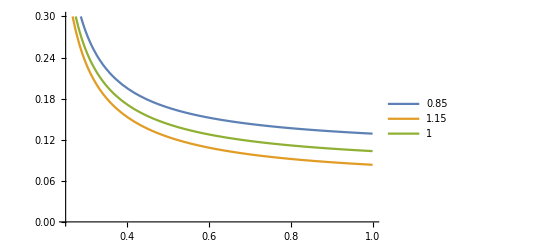

```mathematica
(*Reproducing Figure 3*)
GeV=10^9;
InputParameter={Subscript[N, C]->3,Subscript[α, S]->0.47,Subscript[C, F]->4/3,qqC->(-0.24)^3*GeV^3,ggC->0.012*GeV^4,qGC->0.8*(-0.24)^3*GeV^5};

W[m_,x_]:=1-Sum[(x)^k/k! *Exp[-x],{k,0,m}]

W[2,Subscript[ω, th]/M]

LambdaH=-2*Subscript[α, S]/Pi^3*Subscript[N, C]*Subscript[C, F]*M^5*W[4,Subscript[ω, th]/M]-3*Subscript[α, S]/Pi*Subscript[C, F]*M^2*qqC*W[1,Subscript[ω, th]/M]+M/4*ggC*W[0,Subscript[ω, th]/M]-1/4*qGC;

Plot[{(LambdaH/Formfactor)*10^(-18)/.InputParameter/.Subscript[ω, th]->0.85*GeV,(LambdaH/Formfactor)*10^(-18)/.InputParameter/.Subscript[ω, th]->1.15*GeV,(LambdaH/Formfactor)*10^(-18)/.InputParameter/.Subscript[ω, th]->GeV},{M,0.25*GeV,GeV},PlotLegends->{0.85,1.15,1},PlotRange->{0,0.30}]
```

#### λ_E^2

##### Timelike region ω > 0

```mathematica
Sigma[μ_,ν_]:=I/2*(GA[μ].GA[ν]-GA[ν].GA[μ])
vTensor[μ_,ν_]:=I*(FV[v,μ].GA[ν]-FV[v,ν].GA[μ])
Subscript[Γ, 1]=I*FV[v,ν].FV[v,α].Sigma[μ,α].GA5;
Subscript[Γ, 2]=I*FV[v,σ].FV[v,α].Sigma[ρ,α].GA5;
P=(1+DiracSlash[v])/2;


C1=Subscript[λ, H]^2*TR[Subscript[Γ, 1].P.GA5.Sigma[μ,ν]]+(Subscript[λ, H]^2-Subscript[λ, E]^2)*TR[Subscript[Γ, 1].P.GA5.vTensor[μ,ν]]/.Pair[Momentum[v],Momentum[v]] ->1//Simplify
C2=Subscript[λ, H]^2*TR[GA5.P.Subscript[Γ, 2].Sigma[ρ,σ]]-(Subscript[λ, H]^2-Subscript[λ, E]^2)*TR[GA5.P.Subscript[Γ, 2].vTensor[ρ,σ]]/.Pair[Momentum[v],Momentum[v]] ->1//Simplify

(-I)^2/36*C1*C2
```

6 ⅈ λ_ⅇ^2

6 ⅈ λ_ⅇ^2

λ_ⅇ^4

##### Spacelike region ω < 0

```mathematica
GeV=10^9;
InputParameter={Subscript[N, C]->3,Subscript[α, S]->0.47,Subscript[C, F]->4/3,qqC->(-0.24)^3*GeV^3,ggC->0.012*GeV^4,qGC->0.8*(-0.24)^3*GeV^5};
Sigma[μ_,ν_]:=I/2*(GA[μ].GA[ν]-GA[ν].GA[μ])
vTensor[μ_,ν_]:=I*(FV[v,μ].GA[ν]-FV[v,ν].GA[μ])
Subscript[Γ, 1]=I*FV[v,ν].FV[v,α].Sigma[μ,α].GA5;
Subscript[Γ, 2]=I*FV[v,σ].FV[v,α].Sigma[ρ,α].GA5;
P=(1+DiracSlash[v])/2;


qGCondensate1=I*qGC*ω*Subscript[C, F]*Subscript[α, S]*Log[-ω/μ]/(96*Pi)*((GA[ρ].GA[σ]-GA[σ].GA[ρ]) -2*(FV[v,σ].GA[ρ]-FV[v,ρ].GA[σ]).DiracSlash[v]);
qGCondensate2=I*qGC*ω*Subscript[C, F]*Subscript[α, S]*Log[-ω/μ]/(96*Pi)*((GA[ρ].GA[σ]-GA[σ].GA[ρ]) +2*DiracSlash[v].(FV[v,σ].GA[ρ]-FV[v,ρ].GA[σ]));
qGCondensate=qGCondensate1+qGCondensate2;


(*Der Faktor Pi/Subscript[α, S]in ggC kommt wegen der definition von Gluon Kondensat <Subscript[α, S]/Pi*G^2>*)
uptodim4=TR[Subscript[Γ, 1].P.Subscript[Γ, 2].DiracSlash[v]].LL+TR[Subscript[Γ, 1].P.Subscript[Γ, 2]].QQCondensate*qqC+TR[Subscript[Γ, 1].P.Subscript[Γ, 2].DiracSlash[v]].Coefficient[GGCondensate,DiracSlash[v]]*ggC*Pi/Subscript[α, S]//Contract;


uptodim5=TR[Subscript[Γ, 1].P.Subscript[Γ, 2].DiracSlash[v]].LL+TR[Subscript[Γ, 1].P.Subscript[Γ, 2]].QQCondensate*qqC+TR[Subscript[Γ, 1].P.Subscript[Γ, 2]].QQCondensateDim5*qGC+TR[Subscript[Γ, 1].P.Subscript[Γ, 2].DiracSlash[v]].Coefficient[GGCondensate,DiracSlash[v]]*ggC*Pi/Subscript[α, S]+TR[Subscript[Γ, 1].P.Subscript[Γ, 2].Sigma[μ,ν].qGCondensate]//Contract;



(*====================Imaginary-Part================================*)
uptodim4=uptodim4/.Pair[Momentum[v],Momentum[v]] ->1/.Log[-ω/μ]->(-HeavisideTheta[ω])//Simplify;
uptodim5=uptodim5/.Pair[Momentum[v],Momentum[v]] ->1/.Log[-ω/μ]->(-HeavisideTheta[ω])//Simplify;
(*====================Imaginary-Part================================*)


uptodim4=Integrate[uptodim4*Exp[-ω/M],{ω,0,Subscript[ω, th]},GenerateConditions->False]//Simplify;
uptodim5=Integrate[uptodim5*Exp[-ω/M],{ω,0,Subscript[ω, th]},Assumptions->{0<Subscript[ω, th]<GeV,0<M<GeV},GenerateConditions->False]//Simplify;
```

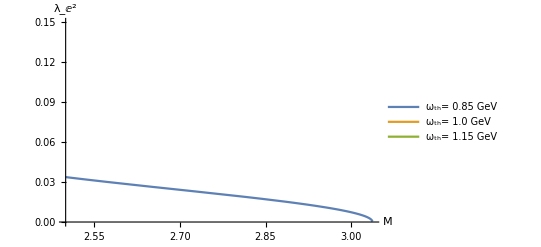

```mathematica
p2=Plot[{Sqrt[(uptodim5/Formfactor)]*10^(-18)/.InputParameter/.Subscript[ω, th]->0.85*GeV,
Sqrt[(uptodim5/Formfactor)]*10^(-18)/.InputParameter/.Subscript[ω, th]->1.0GeV,Sqrt[(uptodim5/Formfactor)]*10^(-18)/.InputParameter/.Subscript[ω, th]->1.15GeV},{M,0.25*GeV,1GeV},PlotLegends->{"ω_th= 0.85 GeV","ω_th= 1.0 GeV"," ω_th= 1.15 GeV"},AxesLabel->{M,Subscript[λ, E]^2},PlotRange->{0,0.15}]
```

```mathematica
Sqrt[(uptodim5/Formfactor)]*10^(-18)/.InputParameter/.Subscript[ω, th]->1.0GeV/.M->0.4*GeV
```

0.+0.0501838 ⅈ

#### λ_H^2

##### Timelike region ω >0

```mathematica
Sigma[μ_,ν_]:=I/2*(GA[μ].GA[ν]-GA[ν].GA[μ])
vTensor[μ_,ν_]:=I*(FV[v,μ].GA[ν]-FV[v,ν].GA[μ])
Subscript[Γ, 1]=I*(1/2*Sigma[μ,ν]-FV[v,ν].FV[v,α].Sigma[μ,α]).GA5;
Subscript[Γ, 2]=I*(1/2*Sigma[ρ,σ]-FV[v,σ].FV[v,α].Sigma[ρ,α]).GA5;
P=(1+DiracSlash[v])/2;
(*C1 = -Subscript[λ, H]*TR[Sigma[μ,ν].Subscript[Γ, 1].P.Subscript[Γ, 2].Sigma[ρ,σ]]
C2=Subscript[λ, H]*(Subscript[λ, H]-Subscript[λ, E])*TR[Sigma[μ,ν].Subscript[Γ, 1].P.Subscript[Γ, 2].vTensor[ρ,σ]]
C3=-Subscript[λ, H]*(Subscript[λ, H]-Subscript[λ, E])*TR[vTensor[μ,ν].Subscript[Γ, 1].P.Subscript[Γ, 2].Sigma[ρ,σ]]
C4=(Subscript[λ, H]-Subscript[λ, E])*TR[vTensor[μ,ν].Subscript[Γ, 1].P.Subscript[Γ, 2].vTensor[ρ,σ]]
*)

C1=Subscript[λ, H]*TR[Subscript[Γ, 1].P.GA5.Sigma[μ,ν]]+(Subscript[λ, H]-Subscript[λ, E])*TR[Subscript[Γ, 1].P.GA5.vTensor[μ,ν]]/.Pair[Momentum[v],Momentum[v]] ->1//Simplify;
C2=Subscript[λ, H]*TR[GA5.P.Subscript[Γ, 2].Sigma[ρ,σ]]-(Subscript[λ, H]-Subscript[λ, E])*TR[GA5.P.Subscript[Γ, 2].vTensor[ρ,σ]]/.Pair[Momentum[v],Momentum[v]] ->1//Simplify;

(-I)^2/36*C1*C2//Simplify
```

λ_H^2

##### Spacelike region ω <0

```mathematica
(*TR[Subscript[Γ, 1].P.Subscript[Γ, 2].DiracSlash[v]].Coefficient[GGCondensate,DiracSlash[v]]*ggC*Pi/Subscript[α, S]*)
```

```mathematica
GeV=10^9;
InputParameter={Subscript[N, C]->3,Subscript[α, S]->0.47,Subscript[C, F]->4/3,qqC->(-0.24)^3*GeV^3,ggC->0.012*GeV^4,qGC->0.8*(-0.24)^3*GeV^5};
Sigma[μ_,ν_]:=I/2*(GA[μ].GA[ν]-GA[ν].GA[μ])
vTensor[μ_,ν_]:=I*(FV[v,μ].GA[ν]-FV[v,ν].GA[μ])
Subscript[Γ, 1]=I*(1/2*Sigma[μ,ν]-FV[v,ν].FV[v,α].Sigma[μ,α]).GA5;
Subscript[Γ, 2]=I*(1/2*Sigma[ρ,σ]-FV[v,σ].FV[v,α].Sigma[ρ,α]).GA5;
P=(1+DiracSlash[v])/2;


qGCondensate1=I*qGC*ω*Subscript[C, F]*Subscript[α, S]*Log[-ω/μ]/(96*Pi)*((GA[ρ].GA[σ]-GA[σ].GA[ρ]) +2*(FV[v,σ].GA[ρ]-FV[v,ρ].GA[σ]).DiracSlash[v]);
qGCondensate2=I*qGC*ω*Subscript[C, F]*Subscript[α, S]*Log[-ω/μ]/(96*Pi)*((GA[ρ].GA[σ]-GA[σ].GA[ρ]) +2*DiracSlash[v].(FV[v,σ].GA[ρ]-FV[v,ρ].GA[σ]));


(*qGCondensate1=-I*ω*Subscript[C, F]*Subscript[α, S]*Log[-ω/μ]*(GA[σ].FV[v,ρ]-GA[ρ].FV[v,σ]).DiracSlash[v];
qGCondensate2=-I*ω*Subscript[C, F]*Subscript[α, S]*Log[-ω/μ]*DiracSlash[v].(GA[σ].FV[v,ρ]-GA[ρ].FV[v,σ]);*)

qGCondensate=qGCondensate1+qGCondensate2;

(*Der Faktor Pi/Subscript[α, S]in ggC kommt wegen der definition von Gluon Kondensat <Subscript[α, S]/Pi*G^2>*)
uptodim3=TR[Subscript[Γ, 1].P.Subscript[Γ, 2].DiracSlash[v]].LL+TR[Subscript[Γ, 1].P.Subscript[Γ, 2]].QQCondensate*qqC//Contract;

uptodim4=TR[Subscript[Γ, 1].P.Subscript[Γ, 2].DiracSlash[v]].LL+TR[Subscript[Γ, 1].P.Subscript[Γ, 2]].QQCondensate*qqC+TR[Subscript[Γ, 1].P.Subscript[Γ, 2].DiracSlash[v]].Coefficient[GGCondensate,DiracSlash[v]]*ggC*Pi/Subscript[α, S]//Contract;


uptodim5=TR[Subscript[Γ, 1].P.Subscript[Γ, 2].DiracSlash[v]].LL+TR[Subscript[Γ, 1].P.Subscript[Γ, 2]].QQCondensate*qqC+TR[Subscript[Γ, 1].P.Subscript[Γ, 2]].QQCondensateDim5*qGC+TR[Subscript[Γ, 1].P.Subscript[Γ, 2].DiracSlash[v]].Coefficient[GGCondensate,DiracSlash[v]]*ggC*Pi/Subscript[α, S]+TR[Subscript[Γ, 1].P.Subscript[Γ, 2].Sigma[μ,ν].qGCondensate]//Contract;


(*====================Imaginary-Part================================*)
uptodim3=uptodim3/.Pair[Momentum[v],Momentum[v]] ->1/.Log[-ω/μ]->(-HeavisideTheta[ω])//Simplify;
uptodim4=uptodim4/.Pair[Momentum[v],Momentum[v]] ->1/.Log[-ω/μ]->(-HeavisideTheta[ω])//Simplify;
uptodim5=uptodim5/.Pair[Momentum[v],Momentum[v]] ->1/.Log[-ω/μ]->(-HeavisideTheta[ω])//Simplify;
(*====================Imaginary-Part================================*)

uptodim3=Integrate[uptodim3*Exp[-ω/M],{ω,0,Subscript[ω, th]},Assumptions->{0<Subscript[ω, th]<GeV,0<M<GeV},GenerateConditions->False]//Simplify;
uptodim4=Integrate[uptodim4*Exp[-ω/M],{ω,0,Subscript[ω, th]},Assumptions->{0<Subscript[ω, th]<GeV,0<M<GeV},GenerateConditions->False]//Simplify;
uptodim5=Integrate[uptodim5*Exp[-ω/M],{ω,0,Subscript[ω, th]},Assumptions->{0<Subscript[ω, th]<GeV,0<M<GeV},GenerateConditions->False]//Simplify;
```

(ⅈ qGC ω (N_C^2-1) α_S log(-ω/μ) ((γ̄)^ρ.(γ̄)^σ-(γ̄)^σ.(γ̄)^ρ+2 ((v̄)^σ.(γ̄)^ρ-(v̄)^ρ.(γ̄)^σ).(γ̄·v̄)))/(192 π N_C)

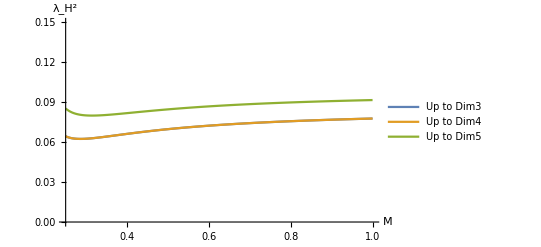

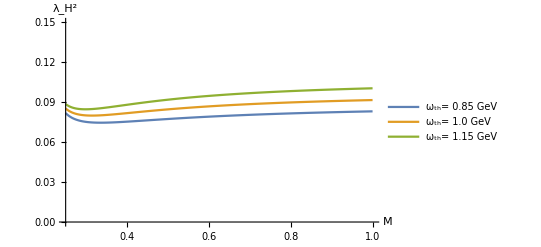

```mathematica
p1=Plot[{Sqrt[(uptodim3/Formfactor)]*10^(-18)/.InputParameter/.Subscript[ω, th]->1.0GeV,Sqrt[(uptodim4/Formfactor)]*10^(-18)/.InputParameter/.Subscript[ω, th]->1.0GeV,
Sqrt[(uptodim5/Formfactor)]*10^(-18)/.InputParameter/.Subscript[ω, th]->1.0GeV},{M,0.25*GeV,GeV},PlotLegends->{"Up to Dim3","Up to Dim4","Up to Dim5"},PlotRange->{0,0.15},AxesLabel->{M,Subscript[λ, H]^2}]

p2=Plot[{Sqrt[(uptodim5/Formfactor)]*10^(-18)/.InputParameter/.Subscript[ω, th]->0.85*GeV,
Sqrt[(uptodim5/Formfactor)]*10^(-18)/.InputParameter/.Subscript[ω, th]->1.0GeV,Sqrt[(uptodim5/Formfactor)]*10^(-18)/.InputParameter/.Subscript[ω, th]->1.15*GeV},{M,0.25*GeV,GeV},PlotLegends->{"ω_th= 0.85 GeV","ω_th= 1.0 GeV"," ω_th= 1.15 GeV"},PlotRange->{0,0.15},AxesLabel->{M,Subscript[λ, H]^2}]
```

```mathematica
(1-Sqrt[(uptodim3/Formfactor)]/Sqrt[(uptodim5/Formfactor)])*100/.InputParameter/.Subscript[ω, th]->1.0GeV/.M->0.4*GeV
```

30.1864